# Template geographical plot for China, including Taiwan

```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
```

CloudConnect::clver: Connecting to a cloud running an earlier version of the Wolfram Engine: 12.0

```mathematica
list=Normal[ds[Select[#Country["Name"]==="China"||#Country["Name"]==="Taiwan"&],(#AdministrativeDivision/.{Entity["AdministrativeDivision",{"Taiwan","Taiwan"}]->Entity["Country","Taiwan"]})->#ConfirmedCases["LastValue"]&]]
```

{Hubei, China→11177,Zhejiang, China→724,Guangdong, China→683,Henan, China→566,Hunan, China→521,Anhui, China→408,Jiangxi, China→391,Chongqing, China→300,Jiangsu, China→271,Sichuan, China→254,Shandong, China→246,Shanghai, China→193,Beijing, China→191,Fujian, China→159,Guangxi, China→127,Shaanxi, China→116,Hebei, China→113,Yunnan, China→105,Heilongjiang, China→95,Hainan, China→71,Liaoning, China→70,Shanxi, China→66,Gansu, China→51,Tianjin, China→48,Guizhou, China→46,Jilin, China→31,Ningxia, China→28,Neimenggu, China→27,Xinjiang, China→24,Qinghai, China→11,Taiwan→10,Xizang, China→1}

```mathematica
i2c[i_]:=Blend[{White,Purple},Log[1+i]/10.]
```

```mathematica
makeplot[list_]:=GeoGraphics[
Map[{GeoStyling[{EdgeForm[{AbsoluteThickness[1],White}],FaceForm[i2c[Last[#]]]}],Tooltip[First[#]["Polygon"],Column[{First[#]["Name"],Last[#]}]]}&,list],GeoProjection->"Orthographic",GeoRange->Automatic,GeoCenter->Entity["Country","China"],ImageSize->1000,GeoBackground->None,Epilog->Text[Style["2019-nCov\nconfirmed cases\nFebruary 3, 2020",16],Scaled[{.25,.25}]]]
```

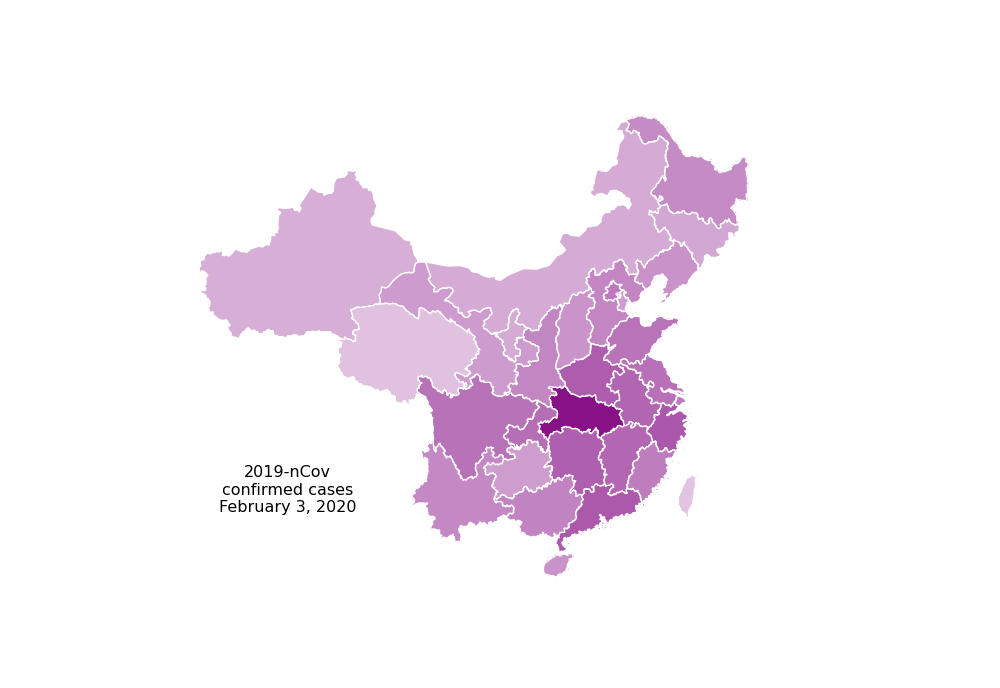

```mathematica
makeplot[list]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\confirmed-cases-02032020.png",ImageCrop[Rasterize[Out[41],"Image",ImageSize->1000]]]
```

D:\git\wolfram-coronavirus\confirmed-cases-02032020.png